```mathematica
Task1EuropeanCallPrices={
{1,1.63676},{2,1.20535},{4,1.25466},{8,1.28154},{16,1.29543},{32,1.30247},{64,1.30601},{128,1.30779}
};
```

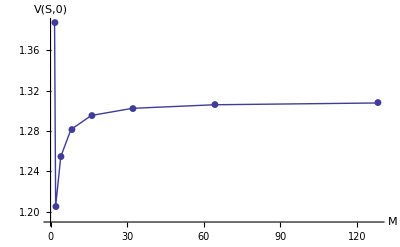

```mathematica
ListPlot[Task1EuropeanCallPrices, AxesOrigin->Automatic, Joined->True, PlotMarkers->Automatic,AxesLabel->{"M","V(S,0)"}]
```

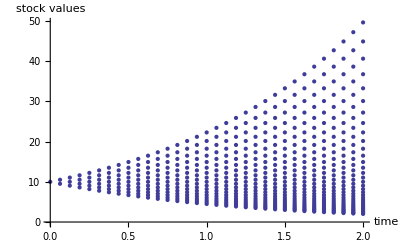

```mathematica
ListPlot[Task1DiscretizationMeshValues,AxesLabel->{"time","stock values"}]
```

```mathematica
Task1DiscretizationMeshValues={
{0,10},{0.0625,9.5116},{0.0625,10.5135},{0.125,9.04705},{0.125,10},{0.125,11.0533},{0.1875,8.6052},{0.1875,9.5116},{0.1875,10.5135},{0.1875,11.6209},{0.25,8.18492},{0.25,9.04705},{0.25,10},{0.25,11.0533},{0.25,12.2176},{0.3125,7.78517},{0.3125,8.6052},{0.3125,9.5116},{0.3125,10.5135},{0.3125,11.6209},{0.3125,12.8449},{0.375,7.40494},{0.375,8.18492},{0.375,9.04705},{0.375,10},{0.375,11.0533},{0.375,12.2176},{0.375,13.5045},{0.4375,7.04328},{0.4375,7.78517},{0.4375,8.6052},{0.4375,9.5116},{0.4375,10.5135},{0.4375,11.6209},{0.4375,12.8449},{0.4375,14.1979},{0.5,6.69929},{0.5,7.40494},{0.5,8.18492},{0.5,9.04705},{0.5,10},{0.5,11.0533},{0.5,12.2176},{0.5,13.5045},{0.5,14.927},{0.5625,6.3721},{0.5625,7.04328},{0.5625,7.78517},{0.5625,8.6052},{0.5625,9.5116},{0.5625,10.5135},{0.5625,11.6209},{0.5625,12.8449},{0.5625,14.1979},{0.5625,15.6934},{0.625,6.06089},{0.625,6.69929},{0.625,7.40494},{0.625,8.18492},{0.625,9.04705},{0.625,10},{0.625,11.0533},{0.625,12.2176},{0.625,13.5045},{0.625,14.927},{0.625,16.4992},{0.6875,5.76487},{0.6875,6.3721},{0.6875,7.04328},{0.6875,7.78517},{0.6875,8.6052},{0.6875,9.5116},{0.6875,10.5135},{0.6875,11.6209},{0.6875,12.8449},{0.6875,14.1979},{0.6875,15.6934},{0.6875,17.3464},{0.75,5.48332},{0.75,6.06089},{0.75,6.69929},{0.75,7.40494},{0.75,8.18492},{0.75,9.04705},{0.75,10},{0.75,11.0533},{0.75,12.2176},{0.75,13.5045},{0.75,14.927},{0.75,16.4992},{0.75,18.2371},{0.8125,5.21551},{0.8125,5.76487},{0.8125,6.3721},{0.8125,7.04328},{0.8125,7.78517},{0.8125,8.6052},{0.8125,9.5116},{0.8125,10.5135},{0.8125,11.6209},{0.8125,12.8449},{0.8125,14.1979},{0.8125,15.6934},{0.8125,17.3464},{0.8125,19.1736},{0.875,4.96079},{0.875,5.48332},{0.875,6.06089},{0.875,6.69929},{0.875,7.40494},{0.875,8.18492},{0.875,9.04705},{0.875,10},{0.875,11.0533},{0.875,12.2176},{0.875,13.5045},{0.875,14.927},{0.875,16.4992},{0.875,18.2371},{0.875,20.1581},{0.9375,4.7185},{0.9375,5.21551},{0.9375,5.76487},{0.9375,6.3721},{0.9375,7.04328},{0.9375,7.78517},{0.9375,8.6052},{0.9375,9.5116},{0.9375,10.5135},{0.9375,11.6209},{0.9375,12.8449},{0.9375,14.1979},{0.9375,15.6934},{0.9375,17.3464},{0.9375,19.1736},{0.9375,21.1932},{1,4.48805},{1,4.96079},{1,5.48332},{1,6.06089},{1,6.69929},{1,7.40494},{1,8.18492},{1,9.04705},{1,10},{1,11.0533},{1,12.2176},{1,13.5045},{1,14.927},{1,16.4992},{1,18.2371},{1,20.1581},{1,22.2814},{1.0625,4.26885},{1.0625,4.7185},{1.0625,5.21551},{1.0625,5.76487},{1.0625,6.3721},{1.0625,7.04328},{1.0625,7.78517},{1.0625,8.6052},{1.0625,9.5116},{1.0625,10.5135},{1.0625,11.6209},{1.0625,12.8449},{1.0625,14.1979},{1.0625,15.6934},{1.0625,17.3464},{1.0625,19.1736},{1.0625,21.1932},{1.0625,23.4255},{1.125,4.06036},{1.125,4.48805},{1.125,4.96079},{1.125,5.48332},{1.125,6.06089},{1.125,6.69929},{1.125,7.40494},{1.125,8.18492},{1.125,9.04705},{1.125,10},{1.125,11.0533},{1.125,12.2176},{1.125,13.5045},{1.125,14.927},{1.125,16.4992},{1.125,18.2371},{1.125,20.1581},{1.125,22.2814},{1.125,24.6283},{1.1875,3.86206},{1.1875,4.26885},{1.1875,4.7185},{1.1875,5.21551},{1.1875,5.76487},{1.1875,6.3721},{1.1875,7.04328},{1.1875,7.78517},{1.1875,8.6052},{1.1875,9.5116},{1.1875,10.5135},{1.1875,11.6209},{1.1875,12.8449},{1.1875,14.1979},{1.1875,15.6934},{1.1875,17.3464},{1.1875,19.1736},{1.1875,21.1932},{1.1875,23.4255},{1.1875,25.8929},{1.25,3.67343},{1.25,4.06036},{1.25,4.48805},{1.25,4.96079},{1.25,5.48332},{1.25,6.06089},{1.25,6.69929},{1.25,7.40494},{1.25,8.18492},{1.25,9.04705},{1.25,10},{1.25,11.0533},{1.25,12.2176},{1.25,13.5045},{1.25,14.927},{1.25,16.4992},{1.25,18.2371},{1.25,20.1581},{1.25,22.2814},{1.25,24.6283},{1.25,27.2225},{1.3125,3.49402},{1.3125,3.86206},{1.3125,4.26885},{1.3125,4.7185},{1.3125,5.21551},{1.3125,5.76487},{1.3125,6.3721},{1.3125,7.04328},{1.3125,7.78517},{1.3125,8.6052},{1.3125,9.5116},{1.3125,10.5135},{1.3125,11.6209},{1.3125,12.8449},{1.3125,14.1979},{1.3125,15.6934},{1.3125,17.3464},{1.3125,19.1736},{1.3125,21.1932},{1.3125,23.4255},{1.3125,25.8929},{1.3125,28.6203},{1.375,3.32338},{1.375,3.67343},{1.375,4.06036},{1.375,4.48805},{1.375,4.96079},{1.375,5.48332},{1.375,6.06089},{1.375,6.69929},{1.375,7.40494},{1.375,8.18492},{1.375,9.04705},{1.375,10},{1.375,11.0533},{1.375,12.2176},{1.375,13.5045},{1.375,14.927},{1.375,16.4992},{1.375,18.2371},{1.375,20.1581},{1.375,22.2814},{1.375,24.6283},{1.375,27.2225},{1.375,30.0899},{1.4375,3.16106},{1.4375,3.49402},{1.4375,3.86206},{1.4375,4.26885},{1.4375,4.7185},{1.4375,5.21551},{1.4375,5.76487},{1.4375,6.3721},{1.4375,7.04328},{1.4375,7.78517},{1.4375,8.6052},{1.4375,9.5116},{1.4375,10.5135},{1.4375,11.6209},{1.4375,12.8449},{1.4375,14.1979},{1.4375,15.6934},{1.4375,17.3464},{1.4375,19.1736},{1.4375,21.1932},{1.4375,23.4255},{1.4375,25.8929},{1.4375,28.6203},{1.4375,31.6349},{1.5,3.00668},{1.5,3.32338},{1.5,3.67343},{1.5,4.06036},{1.5,4.48805},{1.5,4.96079},{1.5,5.48332},{1.5,6.06089},{1.5,6.69929},{1.5,7.40494},{1.5,8.18492},{1.5,9.04705},{1.5,10},{1.5,11.0533},{1.5,12.2176},{1.5,13.5045},{1.5,14.927},{1.5,16.4992},{1.5,18.2371},{1.5,20.1581},{1.5,22.2814},{1.5,24.6283},{1.5,27.2225},{1.5,30.0899},{1.5,33.2593},{1.5625,2.85983},{1.5625,3.16106},{1.5625,3.49402},{1.5625,3.86206},{1.5625,4.26885},{1.5625,4.7185},{1.5625,5.21551},{1.5625,5.76487},{1.5625,6.3721},{1.5625,7.04328},{1.5625,7.78517},{1.5625,8.6052},{1.5625,9.5116},{1.5625,10.5135},{1.5625,11.6209},{1.5625,12.8449},{1.5625,14.1979},{1.5625,15.6934},{1.5625,17.3464},{1.5625,19.1736},{1.5625,21.1932},{1.5625,23.4255},{1.5625,25.8929},{1.5625,28.6203},{1.5625,31.6349},{1.5625,34.9671},{1.625,2.72016},{1.625,3.00668},{1.625,3.32338},{1.625,3.67343},{1.625,4.06036},{1.625,4.48805},{1.625,4.96079},{1.625,5.48332},{1.625,6.06089},{1.625,6.69929},{1.625,7.40494},{1.625,8.18492},{1.625,9.04705},{1.625,10},{1.625,11.0533},{1.625,12.2176},{1.625,13.5045},{1.625,14.927},{1.625,16.4992},{1.625,18.2371},{1.625,20.1581},{1.625,22.2814},{1.625,24.6283},{1.625,27.2225},{1.625,30.0899},{1.625,33.2593},{1.625,36.7626},{1.6875,2.5873},{1.6875,2.85983},{1.6875,3.16106},{1.6875,3.49402},{1.6875,3.86206},{1.6875,4.26885},{1.6875,4.7185},{1.6875,5.21551},{1.6875,5.76487},{1.6875,6.3721},{1.6875,7.04328},{1.6875,7.78517},{1.6875,8.6052},{1.6875,9.5116},{1.6875,10.5135},{1.6875,11.6209},{1.6875,12.8449},{1.6875,14.1979},{1.6875,15.6934},{1.6875,17.3464},{1.6875,19.1736},{1.6875,21.1932},{1.6875,23.4255},{1.6875,25.8929},{1.6875,28.6203},{1.6875,31.6349},{1.6875,34.9671},{1.6875,38.6503},{1.75,2.46094},{1.75,2.72016},{1.75,3.00668},{1.75,3.32338},{1.75,3.67343},{1.75,4.06036},{1.75,4.48805},{1.75,4.96079},{1.75,5.48332},{1.75,6.06089},{1.75,6.69929},{1.75,7.40494},{1.75,8.18492},{1.75,9.04705},{1.75,10},{1.75,11.0533},{1.75,12.2176},{1.75,13.5045},{1.75,14.927},{1.75,16.4992},{1.75,18.2371},{1.75,20.1581},{1.75,22.2814},{1.75,24.6283},{1.75,27.2225},{1.75,30.0899},{1.75,33.2593},{1.75,36.7626},{1.75,40.6349},{1.8125,2.34075},{1.8125,2.5873},{1.8125,2.85983},{1.8125,3.16106},{1.8125,3.49402},{1.8125,3.86206},{1.8125,4.26885},{1.8125,4.7185},{1.8125,5.21551},{1.8125,5.76487},{1.8125,6.3721},{1.8125,7.04328},{1.8125,7.78517},{1.8125,8.6052},{1.8125,9.5116},{1.8125,10.5135},{1.8125,11.6209},{1.8125,12.8449},{1.8125,14.1979},{1.8125,15.6934},{1.8125,17.3464},{1.8125,19.1736},{1.8125,21.1932},{1.8125,23.4255},{1.8125,25.8929},{1.8125,28.6203},{1.8125,31.6349},{1.8125,34.9671},{1.8125,38.6503},{1.8125,42.7214},{1.875,2.22643},{1.875,2.46094},{1.875,2.72016},{1.875,3.00668},{1.875,3.32338},{1.875,3.67343},{1.875,4.06036},{1.875,4.48805},{1.875,4.96079},{1.875,5.48332},{1.875,6.06089},{1.875,6.69929},{1.875,7.40494},{1.875,8.18492},{1.875,9.04705},{1.875,10},{1.875,11.0533},{1.875,12.2176},{1.875,13.5045},{1.875,14.927},{1.875,16.4992},{1.875,18.2371},{1.875,20.1581},{1.875,22.2814},{1.875,24.6283},{1.875,27.2225},{1.875,30.0899},{1.875,33.2593},{1.875,36.7626},{1.875,40.6349},{1.875,44.915},{1.9375,2.11769},{1.9375,2.34075},{1.9375,2.5873},{1.9375,2.85983},{1.9375,3.16106},{1.9375,3.49402},{1.9375,3.86206},{1.9375,4.26885},{1.9375,4.7185},{1.9375,5.21551},{1.9375,5.76487},{1.9375,6.3721},{1.9375,7.04328},{1.9375,7.78517},{1.9375,8.6052},{1.9375,9.5116},{1.9375,10.5135},{1.9375,11.6209},{1.9375,12.8449},{1.9375,14.1979},{1.9375,15.6934},{1.9375,17.3464},{1.9375,19.1736},{1.9375,21.1932},{1.9375,23.4255},{1.9375,25.8929},{1.9375,28.6203},{1.9375,31.6349},{1.9375,34.9671},{1.9375,38.6503},{1.9375,42.7214},{1.9375,47.2213},{2,2.01426},{2,2.22643},{2,2.46094},{2,2.72016},{2,3.00668},{2,3.32338},{2,3.67343},{2,4.06036},{2,4.48805},{2,4.96079},{2,5.48332},{2,6.06089},{2,6.69929},{2,7.40494},{2,8.18492},{2,9.04705},{2,10},{2,11.0533},{2,12.2176},{2,13.5045},{2,14.927},{2,16.4992},{2,18.2371},{2,20.1581},{2,22.2814},{2,24.6283},{2,27.2225},{2,30.0899},{2,33.2593},{2,36.7626},{2,40.6349},{2,44.915},{2,49.646}
};
```